```mathematica
Segments[{Cos[t],Sin[t]},{t,0,Pi},4,AspectRatio->Automatic]
```

Segments[{Cos[t],Sin[t]},{t,0,π},4,AspectRatio→Automatic]

```mathematica
Estimate[{Cos[t],Sin[t]},{t,0,Pi},4]
```

Estimate[{Cos[t],Sin[t]},{t,0,π},4]

```mathematica
Segments[{Cos[t],Sin[t]},{t,0,Pi},48,AspectRatio->Automatic]
Estimate[{Cos[t],Sin[t]},{t,0,Pi},48]
```

Segments[{Cos[t],Sin[t]},{t,0,π},48,AspectRatio→Automatic]

Estimate[{Cos[t],Sin[t]},{t,0,π},48]

```mathematica
f[t_]={Cos[t],Sin[t]};
g[t_]={Cos[t^2],Sin[t^2]};
```

```mathematica
{Cos[t],Sin[t]}
```

{Cos[t],Sin[t]}

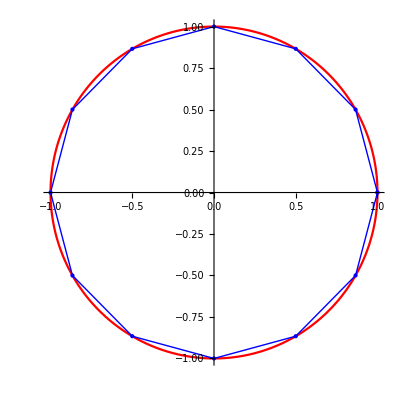

6.21166

```mathematica
Segments[f[t],{t,0,2Pi},12,AspectRatio->Automatic]
Estimate[f[t],{t,0,2Pi},12]
```

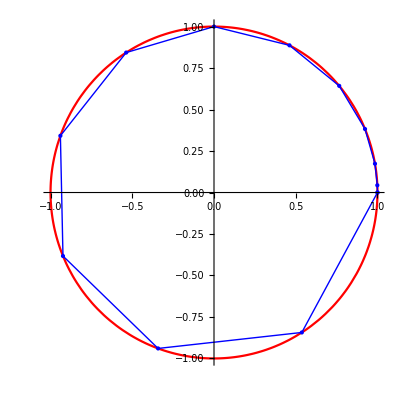

6.14143

```mathematica
Segments[g[t],{t,0,Sqrt[2Pi]},12,AspectRatio->Automatic]
Estimate[g[t],{t,0,Sqrt[2Pi]},12]
```

******************************************
Exercise 2

f(t) = (Cos(t),  Sin(t)),	0≤t≤2π
g(t) = (Cos(t^2), Sin(t^2) ),	0≤t≤√(2π).

abs(f'(T))=√(Cos[t]^2+Sin[t]^2)=1
abs(g'(T))=√(4 t^2 Cos[t]^2+4 t^2 Sin[t]^2)=√((2t)^2)=2t

length1=integral of 1 from 0->2pi=2 π
length2=integral of 2t from 0->√(2 π)=2 π

quadrant 1 esimation of f=1.56072
quadrant 1 esimation of g=1.56428
N[π/2]=1.5708
although g(t) appears as a worse overall estimation of the unit circle since it has more segments in the first quadrant than f(t) it does give a more accurate estimation in the first quadrant.
****************************************

```mathematica
f[t_]={Cos[t],Sin[t]};
g[t_]={Cos[t^2],Sin[t^2]};
```

```mathematica
f'[t]
```

{-Sin[t],Cos[t]}

```mathematica
g'[t]
```

{-2 t Sin[t^2],2 t Cos[t^2]}

```mathematica
absF=Sqrt[(-Sin[t])^(2)+(Cos[t])^(2)]
```

√(Cos[t]^2+Sin[t]^2)

```mathematica
absG=Sqrt[(-2 t Sin[t])^(2)+(2 t Cos[t])^(2)]
```

√(4 t^2 Cos[t]^2+4 t^2 Sin[t]^2)

```mathematica
length1=Integrate[absF,{t,0,2*Pi}]
```

2 π

```mathematica
length2=Integrate[absG,{t,0,Sqrt[2*Pi]}]
```

2 π

```mathematica
Segments[f[t],{t,0,2Pi},12,AspectRatio->Automatic]
Estimate[f[t],{t,0,2Pi},12]
```

-Graphics-

6.21166

```mathematica
Segments[g[t],{t,0,Sqrt[2Pi]},12,AspectRatio->Automatic]
Estimate[g[t],{t,0,Sqrt[2Pi]},12]
```

-Graphics-

6.14143

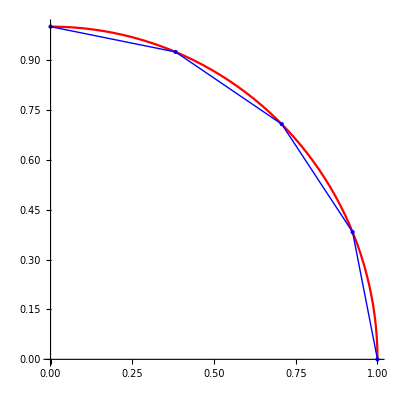

1.56072

```mathematica
Segments[f[t],{t,0,Pi/2},4,AspectRatio->Automatic]
Estimate[f[t],{t,0,Pi/2},4]
```

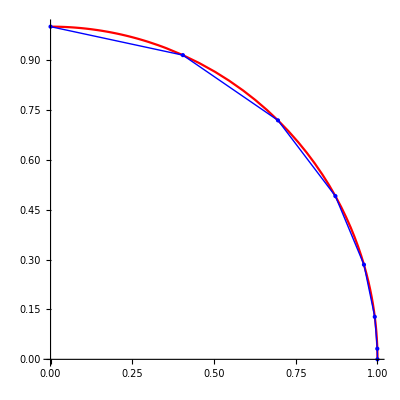

1.56428

```mathematica
Segments[g[t],{t,0,Sqrt[2Pi]/2},7,AspectRatio->Automatic]
Estimate[g[t],{t,0,Sqrt[2Pi]/2},7]
```

```mathematica
N[π/2]
```

1.5708

```mathematica
h[t_]={Cos[t], Sin[t]+0.01 Sin[1000t]}
```

{Cos[t],Sin[t]+0.01 Sin[1000 t]}

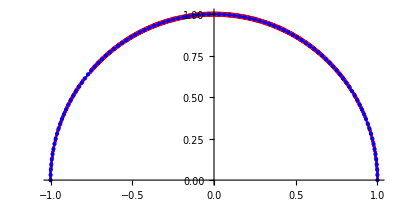

3.14146

```mathematica
Segments[h[t],{t,0,Pi},100]
Estimate[h[t],{t,0,Pi},100]
```

```mathematica
Estimate[h[t],{t,0,Pi},250]
```

3.14157

```mathematica
Estimate[h[t],{t,0,Pi},500]
```

3.14159

```mathematica
NumberForm[3.141587485879561,16]
```

3.141587485879561

```mathematica
Estimate[h[t],{t,0,Pi},1000]
```

3.14159

```mathematica
NumberForm[3.1415913616617215,16]
```

3.141591361661721

```mathematica
Estimate[h[t],{t,0,Pi},950]
```

12.4613

```mathematica
NumberForm[12.461296533313522,16]
```

12.46129653331352

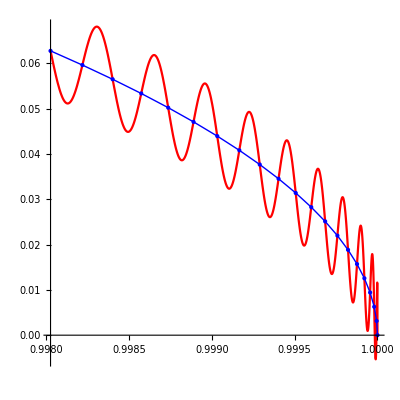

```mathematica
Segments[h[t],{t,0,Pi/50},1000/50,AspectRatio->1]
```

```mathematica
Segments[h[t],{t,0,Pi/50},950/50,AspectRatio->1]
```

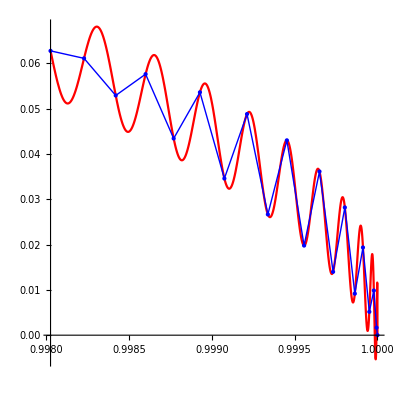

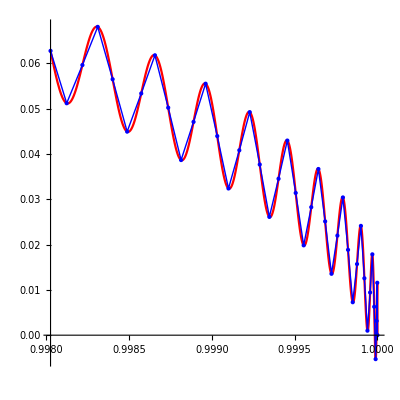
********************
Exercise 3
2000 segments
Segments[h[t],{t,0,Pi/50},2000/50,AspectRatio→1]

-Graphics-

Estimate[h[t],{t,0,Pi/50},2000/50]=0.400007

********************

```mathematica
h[t_]={Cos[t], Sin[t]+0.01 Sin[1000t]}
```

{Cos[t],Sin[t]+0.01 Sin[1000 t]}

```mathematica
Segments[h[t],{t,0,Pi/50},2000/50,AspectRatio->1]
```

-Graphics-

```mathematica
Estimate[h[t],{t,0,Pi/50},2000/50]
```

0.400007

```mathematica
f[t_]={Cos[2*Pi*t],Sin[2*Pi*t],1+t/5}
ParametricPlot3D[f[t],{t,0,10},ViewPoint->{0,-10,1}]
```

{Cos[2 π t],Sin[2 π t],1+t/5}

-Graphics3D-

```mathematica
g[x_,y_,z_]=z
```

z

```mathematica
D[f[t],t]
Norm[%]//Simplify
```

{-2 π Sin[2 π t],2 π Cos[2 π t],1/5}

1/5 √(1+100 π^2)

```mathematica
Apply[g,f[t]]
```

1+t/5

```mathematica
Integrate[Apply[g,f[t]]*Norm[D[f[t],t]],{t,0,10}]
N[%]
```

4 √(1+100 π^2)

125.727

************************
Exersize 5

```mathematica
f[t_]={t,t^2,t^3}
```

{t,t^2,t^3}

```mathematica
D[f[t],t]
```

{1,2 t,3 t^2}

```mathematica
Norm[%]//Simplify
```

√(1+4 t^2+9 t^4)

```mathematica
g[x_,y_,z_]={2x+4y}
```

{2 x+4 y}

```mathematica
Apply[g,f[t]]
```

{2 t+4 t^2}

```mathematica
Integrate[Apply[g,f[t]]*Norm[D[f[t],t]],{t,0,1}]
N[%]
```

{∫_0^1 (2 t+4 t^2) √(1+4 t^2+9 t^4)ⅆt}

{5.76764}